```mathematica
f[x_,r_] =r*x+4*x^3-9*x^5
```

r x+4 x^3-9 x^5

```mathematica
sol = Solve[f[x,r]==0,r]
```

{{r→-4 x^2+9 x^4}}

```mathematica
x/.sol
```

{x}

```mathematica
r
```

r

```mathematica
r/.sol
```

{-4 x^2+9 x^4}

```mathematica
sol=.
```

```mathematica
sol = Solve[f[x,r]==0,r][[1]]
```

{r→-4 x^2+9 x^4}

```mathematica
x/.sol
```

x

```mathematica
r/.sol
```

-4 x^2+9 x^4

```mathematica
r=r/.sol
```

-4 x^2+9 x^4

```mathematica
x/.r
```

ReplaceAll::reps: {-4 x^2+9 x^4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.-4 x^2+9 x^4

```mathematica
sol2 = Solve[f[x,r]==0,x]
```

{{}}

```mathematica
f
```

f

```mathematica
f[x,r]
```

f[x,r]

```mathematica
f[x_,r_] =r*x+4*x^3-9*x^5
```

r x+4 x^3-9 x^5

```mathematica
Solve[f[x,r]==0,x] = sol
```

Set::write: Tag Solve in Solve[r x+4 x^3-9 x^5==0,x] is Protected.

sol

```mathematica
f[x_,r_] =r*x+4*x^3-9*x^5
```

r x+4 x^3-9 x^5

```mathematica
Solve[f[x,r]==0,x] = sol
```

Set::write: Tag Solve in Solve[r x+4 x^3-9 x^5==0,x] is Protected.

sol

```mathematica
Solve[f[x,r]==0,r] = sol
```

Set::write: Tag Solve in Solve[r x+4 x^3-9 x^5==0,r] is Protected.

sol

```mathematica
sol = Solve[f[x,r]==0,x]
```

{{x→0},{x→-1/3 √(2-√(4+9 r))},{x→1/3 √(2-√(4+9 r))},{x→-1/3 √(2+√(4+9 r))},{x→1/3 √(2+√(4+9 r))}}

```mathematica
x_vec = x/.sol
```

{0,-1/3 √(2-√(4+9 r)),1/3 √(2-√(4+9 r)),-1/3 √(2+√(4+9 r)),1/3 √(2+√(4+9 r))}

```mathematica
x1 = 0
```

0

```mathematica
x2=x_vec[1]
```

x_vec[1]

```mathematica
x_vec
```

x_vec

```mathematica
xvec = x/.sol
```

{0,-1/3 √(2-√(4+9 r)),1/3 √(2-√(4+9 r)),-1/3 √(2+√(4+9 r)),1/3 √(2+√(4+9 r))}

```mathematica
x2 = xvec[1]
```

{0,-1/3 √(2-√(4+9 r)),1/3 √(2-√(4+9 r)),-1/3 √(2+√(4+9 r)),1/3 √(2+√(4+9 r))}[1]

```mathematica
x2 = xvec(1)
```

{0,-1/3 √(2-√(4+9 r)),1/3 √(2-√(4+9 r)),-1/3 √(2+√(4+9 r)),1/3 √(2+√(4+9 r))}

```mathematica
x2 = xvec[[1]]
```

0

```mathematica
x2[r_]=xvec[[2]]
```

Set::write: Tag Times in (-1/3 √(2-√(4+9 r)))[r_] is Protected.

-1/3 √(2-√(4+9 r))

```mathematica
x3 = xvec[[3]]
```

1/3 √(2-√(4+9 r))

```mathematica
x4=xvec[[4]]
```

-1/3 √(2+√(4+9 r))

```mathematica
x5 = xvec[[5]]
```

1/3 √(2+√(4+9 r))

```mathematica
yval1 = f[x1,r]
```

0

```mathematica
derFval = D[f[x1,r],x]
```

0

```mathematica
derFVal2 = D[f[x2,r],x]
```

0

```mathematica
df[x_,r_] = D[f[x,r],x]
```

r+12 x^2-45 x^4

```mathematica
dfx1[r_]=df[x1,r]
```

r

```mathematica
dfx2[r_] = df[x2,r]
```

r+4/3 (2-√(4+9 r))-5/9 (2-√(4+9 r))^2

```mathematica
dfx3[r_]= df[x3,r]
```

r+4/3 (2-√(4+9 r))-5/9 (2-√(4+9 r))^2

```mathematica
dfx4[r_] = df[x4,r]
```

r+4/3 (2+√(4+9 r))-5/9 (2+√(4+9 r))^2

```mathematica
dfx5[r_] = df[x5,r]
```

r+4/3 (2+√(4+9 r))-5/9 (2+√(4+9 r))^2

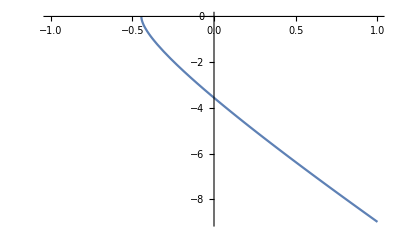

```mathematica
Plot[dfx5[r], {r, -1,1}]
```

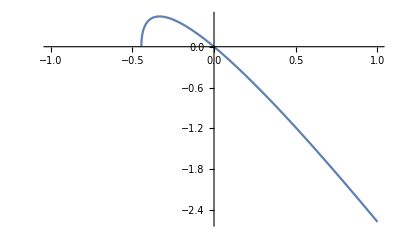
```mathematica
-Graphics-
Plot[f[x3,r], {r, -2, 2}]
```

-Graphics-

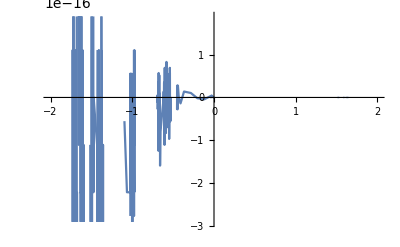

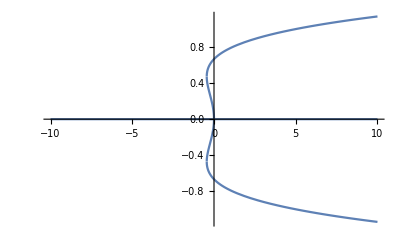

```mathematica
Plot[x/.sol, {r, -10, 10}]
```

```mathematica
f[x,r]
```

r x+4 x^3-9 x^5

```mathematica
plot1 = Plot[HeavisideTheta[-D[f[x,r],x]], {r, -5, 5}]*x/.sol
```

{0,-1/3 √(2-√(4+9 r)) -Graphics-,1/3 √(2-√(4+9 r)) -Graphics-,-1/3 √(2+√(4+9 r)) -Graphics-,1/3 √(2+√(4+9 r)) -Graphics-}

```mathematica
plot2 = Plot[HeavisideTheta[D[f[x,r],x]], {r, -5, 5}]*x/.sol
```

{0,-1/3 √(2-√(4+9 r)) -Graphics-,1/3 √(2-√(4+9 r)) -Graphics-,-1/3 √(2+√(4+9 r)) -Graphics-,1/3 √(2+√(4+9 r)) -Graphics-}

```mathematica
Show[plot1, plot2]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[{0,-1/3 √(2-√(4+9 r)) -Graphics-,1/3 √(2-√(4+9 r)) -Graphics-,-1/3 √(2+√(4+9 r)) -Graphics-,1/3 √(2+√(4+9 r)) -Graphics-},{0,-1/3 √(2-√(4+9 r)) -Graphics-,1/3 √(2-√(4+9 r)) -Graphics-,-1/3 √(2+√(4+9 r)) -Graphics-,1/3 √(2+√(4+9 r)) -Graphics-}]

```mathematica
fprime[x_,r_] = D[f[x,r],x]
```

r+12 x^2-45 x^4

```mathematica
HeavisideTheta[fprime[x,r]]*x/.sol
```

{0,-1/3 √(2-√(4+9 r)) HeavisideTheta[r+4/3 (2-√(4+9 r))-5/9 (2-√(4+9 r))^2],1/3 √(2-√(4+9 r)) HeavisideTheta[r+4/3 (2-√(4+9 r))-5/9 (2-√(4+9 r))^2],-1/3 √(2+√(4+9 r)) HeavisideTheta[r+4/3 (2+√(4+9 r))-5/9 (2+√(4+9 r))^2],1/3 √(2+√(4+9 r)) HeavisideTheta[r+4/3 (2+√(4+9 r))-5/9 (2+√(4+9 r))^2]}

```mathematica
xvec[[2]]
```

-1/3 √(2-√(4+9 r))

```mathematica
sol2[r_]=xvec[[2]]
```

-1/3 √(2-√(4+9 r))

```mathematica
sol3[r_]=xvec[[3]]
```

1/3 √(2-√(4+9 r))

```mathematica
sol4[r_]=xvec[[4]]
```

-1/3 √(2+√(4+9 r))

```mathematica
sol5[r_]=xvec[[5]]
```

1/3 √(2+√(4+9 r))

```mathematica
sol1[r_]=0
```

0

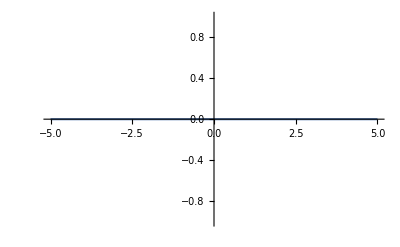

```mathematica
Plot[sol1[r],{r, -5, 5}]
```

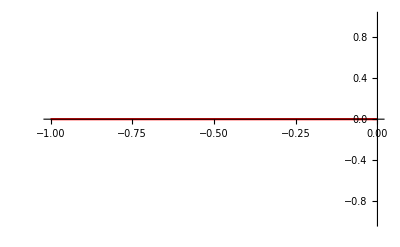

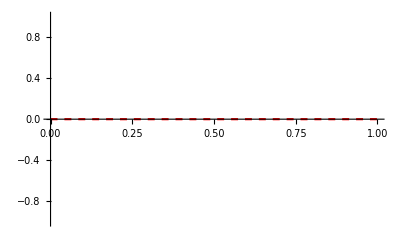

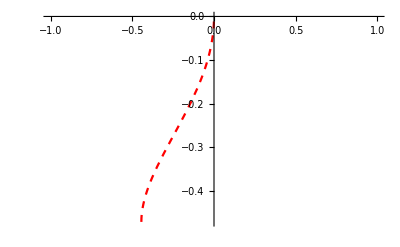

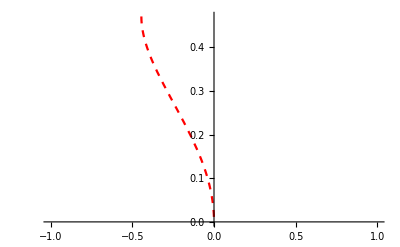

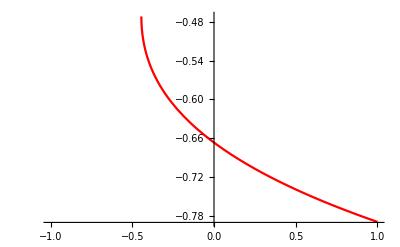

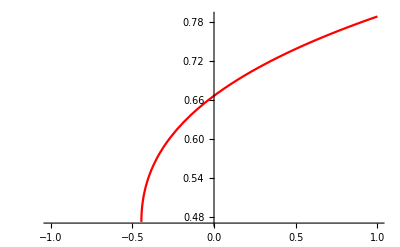

```mathematica
line1 = Plot[sol1[r], {r, -1, 0}, PlotStyle->{Red}]
line2 = Plot[sol1[r], {r, 0, 1}, PlotStyle->{Red, Dashed}]
line3 = Plot[sol2[r], {r, -1, 1}, PlotStyle->{Red, Dashed}]
line4 =  Plot[sol3[r], {r, -1, 1}, PlotStyle->{Red, Dashed}]
line5 =  Plot[sol4[r], {r, -1, 1}, PlotStyle->{Red}]
line6 =  Plot[sol5[r], {r, -1, 1}, PlotStyle->{Red}]
```

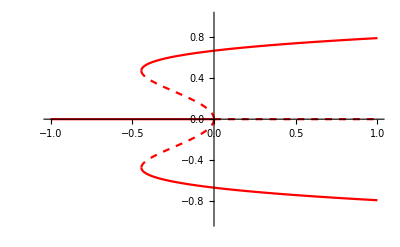

```mathematica
Show[line1,line2,line3,line4, line5,line6, PlotRange-> {{-1,1}, {-1,1}}]
```

```mathematica
f[x,r]
```

r x+4 x^3-9 x^5

```mathematica
Plot[
```